```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

-2.62457×10^-13

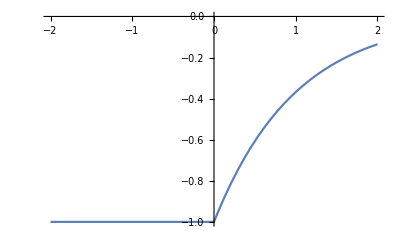

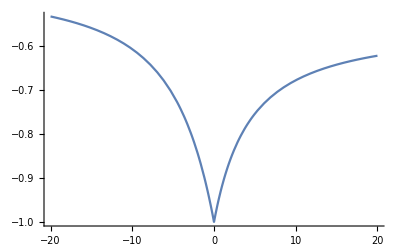

```mathematica
u[x_]:=Module[{W=x},If[W<0,-1,-Exp[-γ W]]] (*for W=x we get infinite position size*)
pr[B_]:=ⅇ^(-B^2/2)/√(2 π)
xx[B_]:= Exp[ σ Sqrt[t] B+(μ-σ^2/2)t];
NIntegrate[xx[B]pr[B],{B,-∞,∞}]-1
Plot[u[W],{W,-2,2}]
γ=1.;μ=0;t=1;σ=.25;
U[a_]:=NIntegrate[u[a (xx[B]-1)]pr[B],{B,-∞,∞}]
Plot[U[a],{a,-20,20}]
```

```mathematica
U2[a_,k_,p_,d_]:=NIntegrate[(
p u[d/p-k+a (xx[B]-1)]+(1-p) u[-d/(1-p)-k+a (xx[B]-1)]
)pr[B],{B,-∞,∞}]
```

```mathematica
d=10;p=.999;d/p
-d/(1-p)
Quiet[FindRoot[U2[0,k,p,d]==U[0],{k,9,11}]]
```

10.01

-10000.

{k→11.}

```mathematica
U2[0,10.010010010010009,p,d]-U[0]
```

1.55431×10^-15

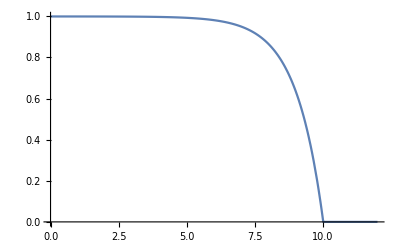

```mathematica
Plot[U2[0,k,p,d]-U[0],{k,0,12},PlotRange-> All]
```

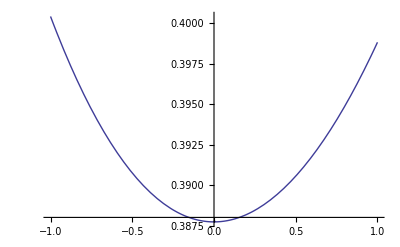

```mathematica
k=0
```